Charles Rambo

# PHY 311 Exam 2: Take Home

In this exam, consider the following non-dimensional system:

		dx/dt = -y - z
		dy/dt = x + ay
		dz/dt = b + z(x-c)
		
Where x, y, and z are functions of time, and a, b, and c are constants.

### 1. General Characteristics of the Model

#### a. Descibe the expected behavior of the system by analyzing each term (growth , decay, oscillation, linear, nonlinear, etc.)

When z = 0 the equations are linear, the z term creates the non-linear behavior for the system. This indicates that the ż function is what creates most of the interesting behavior. When x is larger than c the system will see decay in the ẋ function which will lead to c*z becoming the dominate part of the ż function which assuming a small b doesn’t have much tolerance for this change, and will quickly become negative. Once the ż function is negative, we will start to see growth in the ẋ function. This exchange leads to oscillation. The ẏ function increases as y increases and when x is less than c.  When a is small the ẏ function is dominated by the behavior of x. This all means that we can expect oscillations in all three dimensions, essentially c is contributing to both the damping and the driving depending on how the ż function is behaving.

#### b. Discuss the possibility of chaos.

When z >0, there are three degrees of freedom (x,y,z), and the equations become non-linear as the equations can no longer be written as a linear combination, these are the two attributes necessary for chaotic behavior. We can also expect to see a sensitivity o initial conditions, which is characteristic of chaos because in the conditions described above, there is likely to be great variance depending on how x_0, y_0, and z_0 are defined.

### 2. Mathematica Simulation

#### a. Conduct a suite of simulations with a = b = 0.100. Vary c between 4.00 and 9.00. Plot x-y phase space and Poincare map for these simulations. Choose your own initial conditions.

***Note, in the below plots tf must be greater than ti at this point plots will begin to be made. I made the bulk of my observations by zooming as far into these graphs as the computer would allow.***

```mathematica
a=b=0.100
x0=0
y0=0
z0=0
```

0.1

0

0

0

```mathematica
Manipulate[
With[{solution = NDSolve[
{x'[t] == - y[t] - z[t],
y'[t] == x[t]+a*y[t],
z'[t] == b+z[t]*x[t]-c*z[t],
x[0] == x0,
y[0] == y0,
z[0] == z0},
   {y, x, z}, {t, ti, tf}]},
Plot[
Evaluate[x[t]/.solution],{t,ti, tf} ,
AxesLabel -> {"t", "x"},
PlotTheme->"Detailed"]]
,{ti,0,5000},{tf,ti,5000},{c,4,9}]
Manipulate[
With[{solution = NDSolve[
{x'[t] == - y[t] - z[t],
y'[t] == x[t]+a*y[t],
z'[t] == b+z[t]*x[t]-c*z[t],
x[0] == x0,
y[0] == y0,
z[0] == z0},
   {y, x, z}, {t, ti, tf}]},
ParametricPlot[
Evaluate[{x[t], y[t]} /.solution],{t,ti, tf} ,
AxesLabel -> {"x", "y"},
PlotRange->Full,
PlotStyle->Thin,
PlotTheme->"Detailed"
PlotLabel -> "x-y"] ]
,{ti,0,5000},{tf,ti,5000},{c,4,9}]
```

NDSolve::ndnl: Endpoint  in {t,0.,} is not a real number.

ReplaceAll::reps: {NDSolve[{x'[t]==-y[t]-z[t],y'[t]==x[t]+0.1 y[t],z'[t]==0.1-4 z[t]+x[t] z[t],x[0]==0,y[0]==0,z[0]==0},{y,x,z},{t,0,}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Plot::plln: Limiting value  in {t,0,} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

NDSolve::ndnl: Endpoint  in {t,0.,} is not a real number.

ReplaceAll::reps: {NDSolve[{x'[t]==-y[t]-z[t],y'[t]==x[t]+0.1 y[t],z'[t]==0.1-4 z[t]+x[t] z[t],x[0]==0,y[0]==0,z[0]==0},{y,x,z},{t,0,}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ParametricPlot::plln: Limiting value  in {t,FE`ti$$29,FE`tf$$29} is not a machine-sized real number.

NDSolve::ndnl: Endpoint  in {t,340.,} is not a real number.

ReplaceAll::reps: {NDSolve[{x'[t]==-y[t]-z[t],y'[t]==x[t]+0.1 y[t],z'[t]==0.1-4 z[t]+x[t] z[t],x[0]==0,y[0]==0,z[0]==0},{y,x,z},{t,340.,}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Plot::plln: Limiting value  in {t,340.,} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

4

120

500

{{y→InterpolatingFunction[{{120., 500.}}, <>],x→InterpolatingFunction[{{120., 500.}}, <>],z→InterpolatingFunction[{{120., 500.}}, <>]}}

{2. ArcTan[Tan[0.5 Mod[InterpolatingFunction[{{120., 500.}}, <>][t],2 π]]]}

{InterpolatingFunction[{{120., 500.}}, <>][t]}

40

3000

5.9986

30

-30

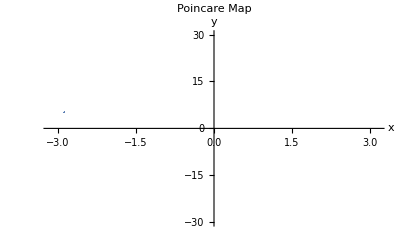

```mathematica
c1=4
ti=120
tf=500
solution = NDSolve[
{x'[t] == - y[t] - z[t],
y'[t] == x[t]+a*y[t],
z'[t] == b+z[t]*x[t]-c1*z[t],
x[0] == x0,
y[0] == y0,
z[0] == z0},
   {y, x, z}, {t, ti, tf}]
x1 = 2.0 ArcTan[Tan[0.5Mod[x[t] /. solution, 2 Pi]]]
y1 = y[t] /. solution
 
MaxTime = 40 
NumberPoints = 3000
PoincareInterval =5.9986

MaxY = 30
MinY = -30

x1y1Poincare= Partition[Flatten[Table[{x1, y1}, {t, ti, tf, PoincareInterval}]],2];
ListPlot[x1y1Poincare, AxesLabel -> {"x", "y"}, PlotRange->{ {-Pi,Pi}, {MinY,MaxY}}, PlotLabel -> "Poincare Map" , PlotStyle -> PointSize[.002]]
```

5.351

2000

2200

{{y→InterpolatingFunction[{{2000., 2200.}}, <>],x→InterpolatingFunction[{{2000., 2200.}}, <>],z→InterpolatingFunction[{{2000., 2200.}}, <>]}}

{2. ArcTan[Tan[0.5 Mod[InterpolatingFunction[{{2000., 2200.}}, <>][t],2 π]]]}

{InterpolatingFunction[{{2000., 2200.}}, <>][t]}

12.044

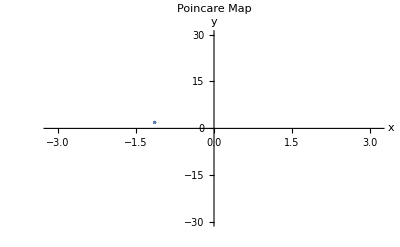

```mathematica
c2=5.351
ti=2000
tf=2200
solution = NDSolve[
{x'[t] == - y[t] - z[t],
y'[t] == x[t]+a*y[t],
z'[t] == b+z[t]*x[t]-c2*z[t],
x[0] == x0,
y[0] == y0,
z[0] == z0},
   {y, x, z}, {t, ti, tf}]
x1 = 2.0 ArcTan[Tan[0.5Mod[x[t] /. solution, 2 Pi]]]
y1 = y[t] /. solution
 
PoincareInterval =12.044

ListPlot[x1y1Poincare, AxesLabel -> {"x", "y"}, PlotRange->{ {-Pi,Pi}, {MinY,MaxY}}, PlotLabel -> "Poincare Map" , PlotStyle -> PointSize[.005]]
```

7.756

3000

3200

{{y→InterpolatingFunction[{{3000., 3200.}}, <>],x→InterpolatingFunction[{{3000., 3200.}}, <>],z→InterpolatingFunction[{{3000., 3200.}}, <>]}}

{2. ArcTan[Tan[0.5 Mod[InterpolatingFunction[{{3000., 3200.}}, <>][t],2 π]]]}

{InterpolatingFunction[{{3000., 3200.}}, <>][t]}

21.1966

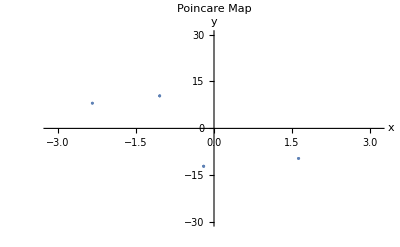

```mathematica
c3=7.756
ti=3000
tf=3200
solution = NDSolve[
{x'[t] == - y[t] - z[t],
y'[t] == x[t]+a*y[t],
z'[t] == b+z[t]*x[t]-c3*z[t],
x[0] == x0,
y[0] == y0,
z[0] == z0},
   {y, x, z}, {t, ti, tf}]
x1 = 2.0 ArcTan[Tan[0.5Mod[x[t] /. solution, 2 Pi]]]
y1 = y[t] /. solution

PoincareInterval =21.19662

x1y1Poincare= Partition[Flatten[Table[{x1, y1}, {t, ti, tf, PoincareInterval}]],2];
ListPlot[x1y1Poincare, AxesLabel -> {"x", "y"}, PlotRange->{ {-Pi,Pi}, {MinY,MaxY}}, PlotLabel -> "Poincare Map" , PlotStyle -> PointSize[.005]]
```

#### b. Describe the dynamics of the system. Make sure to distinguish between the transient phase and the “steady-state” phase. Discuss how and why the behavior changes as c varies.

In varying c, one thing that seems to change is how quickly the system reaches steady state. For c=4 the system seems to leave transience very close to t=120, but for c=5.351 I was still having trouble with transience. 

more importantly this variable controls the number of periods in the system. It appears that from c values between 4 and 5.351 there is only one period, and at about 7.756 we see the period start to double again. I did not spend a lot of time finding an exact value, but at around 8.6 we see the another period doubling, and at c = 9 the system becomes chaotic.

These attributes can be seen in both the parametric plot as well as the Poincare map, and are easier to identify after the transient time has passed. In the Poincare map all of the dots are in the same spot, and the parametric x-y position follows the same path.

It is difficult to say the least to use the Poincare map for making observations in this system, as a new Poincare interval is necessary for every c value if any insights are to be made. I have attempted to use the Poincare Maps above as a tool for confirming the start of period doubling, but even in the third map (c_2 to c_3) we can see that it might not be useful for that as both the x vs t plot and x vs y plots show that it happens very close, to t=7.756 and the period should be close to 2.197.

The behavior of this system varies with c because of the relation z(x-c) which means that as the x term over takes c the behavior of the system changes as described in part 1a. As such x must do more to be the dominate term. What this leads to is longer periods of time where each part dominates, which can be seen from the longer Poincare intervals used for the Poincare plots.

#### c. Estimate the Feignbaum number for this system.

```mathematica
δ=(c2-c1)/(c3-c2)
```

0.561746

If the above is true we should be able to use it to calculate roughly where the next doubling occurs.

```mathematica
c4=1/δ(c3-c2)+c3
```

12.0373

Obviously this returns a value well above what I would expect for the next doubling. (***Note to Dr. Baker I have just realize this issue at 14.09 on 17.11, I will endeavor to correct it, I feel that the issue is either in my c3, or my assumption that c=4 represents to start of a single period***)

```mathematica
c4=8.52
δ=(c3-c2)/(c4-c3)
```

8.52

3.14791

Using our new number I hope to find another visible period doubling before chaos...

```mathematica
c5=1/δ(c4-c3)+c4
```

8.7627

This seems to work. my c5 is a little high, as the doubling appears to happen closer to 8.76. I largely blame this in accuracy on my hasty finding of both c4, and c5. This seems weirdly close to π. In fact using it instead of my delta initially seems to yield better results. I wish I had noticed this earlier as investigation may have lead to more interesting insights, or then again it could have lead down a rabbit’s hole.

```mathematica
c4=1/Pi(c3-c2)+c3
```

8.52154

#### d. Vary initial conditions slightly and discuss the result.:

```mathematica
Manipulate[
With[{solution = NDSolve[
{x'[t] == - y[t] - z[t],
y'[t] == x[t]+a*y[t],
z'[t] == b+z[t]*x[t]-c*z[t],
x[0] == x0,
y[0] == y0,
z[0] == z0},
   {y, x, z}, {t, 0, tf}]},
ParametricPlot[
Evaluate[{x[t], y[t]} /.solution],{t,0, tf} ,
AxesLabel -> {"x", "y"},
PlotRange->Full,
PlotLabel -> "x-y"] ]
,{z0,0,100},{y0,0,100},{x0,0,100},{tf,0.1,1000},{c,4,9}]
```

##### i. For thw simplest system behavior.

I argue that the simplest system exists around initial conditions x_0= .78, y_0= 5.46,  z_0= 1.68 for c = 4.This will of course change as c changes, however with these variables essentially no transient phase exists. In fact inputting the values c from before there is still little to no transient phase. If I had messed with this sooner it is possible that this would have been an easier, or perhaps more precise way to find the points for period doubling (in hind sight, “choose your initial conditions,” may have been a hint.

##### ii. For the most complex sytem behavior.

While it would be easy to argue for the most complex system to involve a chaotic c (i.e. c = 9), I feel that for the spirit of the question, which only asks about varying the initial conditions, c should be held to 4, this has the added benefit that it keeps the transient phase low so a truer complexity for the system may be found. When the initial conditions are changed to values beyond the attractor ‘loops’ seem to fall off of the phase space plot. This appears to be a different type of transience as essentially the plot returns to the attractor. This makes sense sense to me, as there must be a ‘damping’ term that holds the the system to the attractor. The damping would also serve the purpose of decreasing the contribution of the initial values as time gets larger.

#### e. Compare the behavior of this system with that of the driven, damped, nonlinear pendulum.

Based upon the discoveries that I believe I have made in this, the biggest difference is that as written there is a single term that controls the damping and driving.This is the ż function, which it’s self is controlled largely by the value of c. In the DDP, we see that there is a driving term f(t), and the damping 2β term is separate. f(t) also works to bound the system to a sinusoidal relation, where as clearly tit is the ẋ, ẏrelations that bounds this system as indicated by their sinusoidal relation, which we do not see in the graphs below. This is related to the observation above when z=0. This relation that develops is similar to the conditions that create the oscillations in the DDP.

What we also saw with the DDP was that the Poincare map was much more useful (I think this is related to the above observation). We were able to hold the Poincare interval constant will making adjustments to the driving term and see how that affected chaotic behavior. 

I feel that this alone should show that c is responsible for the driving and and damping as it was necessary for the calculation of the δ for this system, as well as the Poincare interval which relates to the natural frequency of the system, and controls the damping constant. 

Another superfluous observation of his system is that while I haven’t been able to get it to graph in any meaningful way, there will be movement in 3 dimensions, where as the DDP is limited to the x-y plane.

4

{{y→InterpolatingFunction[{{0., 500.}}, <>],x→InterpolatingFunction[{{0., 500.}}, <>],z→InterpolatingFunction[{{0., 500.}}, <>]}}

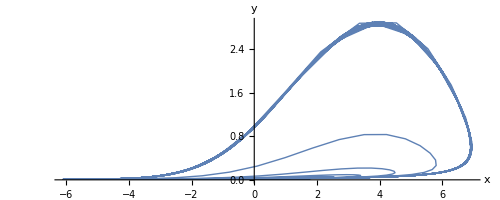

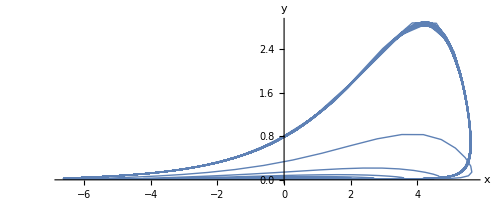

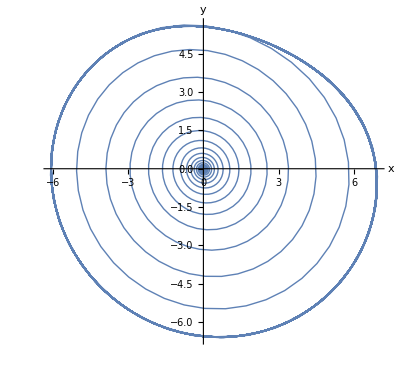

-Graphics-

-Graphics-

```mathematica
c=4
solution = NDSolve[
{x'[t] == - y[t] - z[t],
y'[t] == x[t]+a*y[t],
z'[t] == b+z[t]*x[t]-c*z[t],
x[0] == x0,
y[0] == y0,
z[0] == z0},
   {y, x, z}, {t, 0, 500}]
ParametricPlot[
Evaluate[{x[t], z[t]} /.solution],{t,0, 500} ,
AxesLabel -> {"x", "y"},
PlotRange->Full,
PlotStyle->Thin,
PlotTheme->"Detailed"
PlotLabel -> "x-y"] 
ParametricPlot[
Evaluate[{y[t], z[t]} /.solution],{t,0, 500} ,
AxesLabel -> {"x", "y"},
PlotRange->Full,
PlotStyle->Thin,
PlotTheme->"Detailed"
PlotLabel -> "x-y"] 
ParametricPlot[
Evaluate[{x[t], y[t]} /.solution],{t,0, 500} ,
AxesLabel -> {"x", "y"},
PlotRange->Full,
PlotStyle->Thin,
PlotTheme->"Detailed"
PlotLabel -> "x-y"] 
Plot[y[t],{t,0,130}]
Plot[z[t],{t,0,130}]
```